# Wolfram语言专题讲座 机器学习和人工智能

杨圣汇 Wolfram Research Inc

-Graphics-

## 提纲

### 特征抓取

Wolfram语言函数：FeatureExtract

FeatureExtractor 中的方法选项

### 降低维度

Wolfram语言函数：DimensionReduce

在二维或者三维特征空间中探索数据

### 聚类算法

Wolfram语言中的聚类函数

通过聚类算法来进行分类

### 主成分分析简介

限制

原理和示例

## 特征抓取

所有的机器学习算法的输入都是向量，数组或者张量。

-Graphics-

FeatureExtract 可以从多种数据类型中抓取信息，包括数值，文本，声音和图像以及它们的混合类型.

把名义特征（定性描述的文本）转化为数字

```mathematica
FeatureExtract[{{"Yes","A"},{"No","A"},{"No","B"},{"Maybe","B"},{"No", "C"}}]
```

{{1.92678,1.65441,0.595317,-0.624595,-1.16134,0.760573},{-0.308638,-0.776307,0.467408,-0.624582,-1.16134,0.76057},{-0.30864,-0.776307,0.467411,1.20164,0.484305,-1.22256},{-1.00086,0.674512,-1.99754,1.20163,0.484316,-1.22256},{-0.308641,-0.776309,0.467408,-1.15409,1.35406,0.923982}}

转换布尔类型

```mathematica
FeatureExtract[{{1,True},{2,True},{2,False},{1,False}}]
```

{{-1.,-1.00001,-1.},{1.,-0.999995,-1.},{1.,0.999995,1.},{-1.,1.,1.}}

从图片中抓取数值特征

```mathematica
FeatureExtract[{-Graphics-,-Graphics-,-Graphics- ,-Graphics-,-Graphics-,-Graphics-}]
```

{{16.9775,1.43446,3.41155,10.0882,21.6653},{8.51812,13.1914,11.741,12.4947,-17.493},{22.9647,-10.6604,-12.6311,-14.1652,-7.76728},{-15.2264,-20.7143,18.8287,-3.86606,-0.1173},{-19.4959,-3.95764,-21.8003,12.8176,-1.52362},{-13.7381,20.7065,0.450134,-17.3692,5.23589}}

## 特征抓取方法: 标准化数值特征

该数据样本每一个列的特征的数值跨度均不相同

```mathematica
mat = Transpose[{RandomInteger[5,10],RandomReal[1,10],RandomChoice[Range[100],10]}];
mat//MatrixForm
```

(0 | 0.0216169 | 37
0 | 0.0540866 | 85
4 | 0.170687 | 85
1 | 0.118414 | 36
4 | 0.235657 | 80
0 | 0.495924 | 17
3 | 0.0907073 | 88
2 | 0.807906 | 96
1 | 0.140714 | 2
5 | 0.791486 | 56)

产生一个标准化的特征向量（平均值为0，方差/标准差为1）

```mathematica
fvmat =FeatureExtract[mat,"StandardizedVector"]
```

{{-1.11803,-0.959475,-0.669346},{-1.11803,-0.84456,0.846155},{1.11803,-0.431892,0.846155},{-0.559017,-0.616895,-0.700919},{1.11803,-0.201954,0.68829},{-1.11803,0.719169,-1.3008},{0.559017,-0.714953,0.940873},{0.,1.82332,1.19346},{-0.559017,-0.537973,-1.7744},{1.67705,1.76521,-0.0694604}}

检查每一列的平均值

```mathematica
Chop[Mean[fvmat]]
```

{0,0,0}

检查每一列的标准差

```mathematica
StandardDeviation[fvmat]
```

{1.05409,1.05409,1.05409}

## 特征抓取方法: 文本到数值类型转化

把文本转化为数值

```mathematica
NetEncoder["Characters"]@"the cat is grey"
```

{87,75,72,3,70,68,87,3,76,86,3,74,85,72,92}

```mathematica
NetEncoder["Tokens"]@"the cat is grey"
```

{34556,5052,18459,39265}

```mathematica
FeatureExtract[{"the cat is grey","my cat is fast","this dog is scary","the big dog"}]
```

{{-1.03721,-1.22635,2.19043},{-2.79602,-0.266957,-1.63574},{0.851446,3.0376,0.304013},{2.98179,-1.54429,-0.858706}}

```mathematica
c=Classify[{"The cat is grey."->-Graphics-,"My cat is fast."->-Graphics-,"This dog is scary."->-Graphics- ,"The big dog."->-Graphics-},FeatureExtractor->{ToUpperCase, RemoveDiacritics,"SegmentedWords"}]
```

ClassifierFunction[…]

```mathematica
c[{"Nice CAT","What a dög"}]
```

{-Graphics-,-Graphics-}

指明抓取器使用逆向文本频率

```mathematica
FeatureExtract[{"the cat is grey","my cat is fast","this dog is scary","the big dog"},"TFIDF"]
```

先将文本分成词，然后再转码为整数列表

```mathematica
FeatureExtract[{"the cat is grey","my cat is fast","this dog is scary","the big dog"},{"SegmentedWords","IntegerVector"}]
```

{{11,7,5,7,2,7,6},{10,7,5,7,2,7,8},{4,7,1,7,2,7,3},{11,7,9,7,1}}

## 维度降低法/Embedding

维度降低可视为特征提取和选择的特殊情况，其中数据的投影维度与原特征空间不同。

当给定数据的特征维度太高的时候，把特征映射到低纬度空间有以下几个好处

避免维数灾难 - 一般来讲过拟合的模型的性能非常低下

二维或者三维的特征空间更容易可视化，可以帮助我们探究与分析

一个常用的法则是 样本数量 = 10 x 特征数量 （尽量避免拥挤问题）

DimensionReduce 把数据映射到低维近似流形上面

```mathematica
DimensionReduce[{"the cat is grey","my cat is fast","this dog is scary","the big dog"}]
```

自动降维度

```mathematica
flowers = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
reduced = DimensionReduce[flowers, 2];
```

```mathematica
reduced
```

{{-19.7772,25.6661},{-4.21945,41.3735},{-19.4827,19.1779},{-35.2321,1.5771},{-45.7432,4.57804},{-17.5393,19.2883},{-11.7713,-23.8427},{-20.2746,-16.8694},{-21.5447,-24.9094},{26.5859,6.74013},{74.4563,-0.5469},{11.6288,-4.98266},{28.149,-1.06014},{50.9785,-2.39774},{5.55013,0.443553},{52.4223,-0.513103},{-26.7549,-18.0658},{-10.3037,-21.494},{-15.8792,3.64608},{-6.78219,0.647646},{5.53374,-8.45656}}

把原空间数据绘制在二维空间

```mathematica
ListPlot[Thread[reduced-> flowers], LabelingFunction->Callout[Automatic,Automatic]]
```

-Graphics-

降维技术可以分为线性和非线性两大类

指定主成分分析法降维

```mathematica
reduced = DimensionReduce[flowers, 2, Method->"PrincipalComponentsAnalysis"];
ListPlot[Thread[reduced-> flowers], LabelingFunction->Callout[Automatic,Automatic]]
```

-Graphics-

指定 TSNE 方法降维 （随机近邻嵌入）

```mathematica
reduced = DimensionReduce[flowers, 2, Method->"TSNE"];
ListPlot[Thread[reduced-> flowers], LabelingFunction->Callout[Automatic,Automatic]]
```

-Graphics-

线上仿真 https://distill.pub/2016/misread-tsne/

其他例子

```mathematica
pts=;
reduced=Flatten@DimensionReduce[pts,1,PerformanceGoal->"Quality",Method->"TSNE" (*t-Distributed Stochastic Neighbor Embedding*)];
Manipulate[Row[{ListPlot[pts,Epilog->{PointSize[0.04],Point[pts[[i]]]},ImageSize->500],Graphics[{PointSize[0.04],Point[{reduced[[i]],0}]},Axes->{True,False},AspectRatio->1/5,PlotRange->{MinMax[reduced],Automatic},ImageSize->500]}],
{i,1,Length[pts],1},SaveDefinitions->True]
```

```mathematica
shape=N@Position[ImageData@-Graphics-,1,{2}];
```

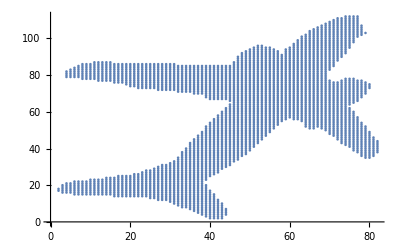

```mathematica
ListPlot[shape]
```

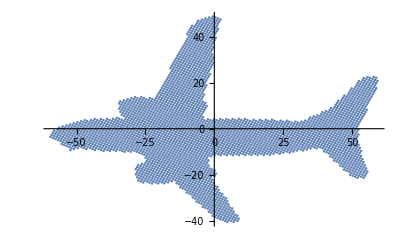

```mathematica
ListPlot[PrincipalComponents[shape]]
```

## 探究特征空间

FeatureSpacePlot 自动抓取特征，并在二维平面上绘制

把相似的鲜花图片归类在一起，并将它们绘制在二维平面上

```mathematica
FeatureSpacePlot[flowers]
```

-Graphics-

## 聚类算法

FindClusters 将一列由正负数构成的数列进行归类

```mathematica
FindClusters[{-7,-7,-5,-5,-10,-10,-5,-10,-9,-8,-10,-9,-8,-7,5,6,7,8,5,10,3,10,5,4,4,2,3,4}]
```

{{-7,-7,-5,-5,-10,-10,-5,-10,-9,-8,-10,-9,-8,-7},{5,6,7,8,5,10,3,10,5,4,4,2,3,4}}

明确指定类别的个数

```mathematica
images={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
FindClusters[images,3]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

产生一个由随机颜色构成的数据样本

```mathematica
colors = RandomColor[30]
```

{RGBColor[0.5964686797062586, 0.4154273239149413, 0.002304993332336025],RGBColor[0.544320733005607, 0.3267667386219941, 0.6091726555178045],RGBColor[0.08790766685325413, 0.1361568307330927, 0.5388146559209095],RGBColor[0.3531364757979971, 0.7840280073034662, 0.5905070484451527],RGBColor[0.2708354097301511, 0.5744422523889012, 0.5230722845416991],RGBColor[0.44446720495072856, 0.9006593961954843, 0.6024439357640361],RGBColor[0.6845054657724166, 0.13160248710678535, 0.7893876685938452],RGBColor[0.6375189338677563, 0.8719623407871384, 0.0726392046722737],RGBColor[0.9439718273448432, 0.36782999192160615, 0.11103474939065539],RGBColor[0.7424822809611042, 0.8218676289808728, 0.8104149988176665],RGBColor[0.4497712757279879, 0.6418642726610326, 0.004229185739978103],RGBColor[0.3892298002668382, 0.3610014182204937, 0.4175845603359871],RGBColor[0.2730029305842354, 0.25989731669356564, 0.3476133652058979],RGBColor[0.8447829395125954, 0.3414241680846164, 0.20107148288700682],RGBColor[0.3955042336852086, 0.9808376656017574, 0.7305447823237341],RGBColor[0.4259317886575673, 0.089767882621971, 0.29107492951100733],RGBColor[0.4681439878403937, 0.0581764592669356, 0.4950112498297139],RGBColor[0.9427730558752825, 0.5093758063744183, 0.25727929710786457],RGBColor[0.5981246873778734, 0.6707629392824686, 0.6141088100885357],RGBColor[0.8572754779644729, 0.5573341698820553, 0.5094364625415542],RGBColor[0.9180215980546009, 0.38983577542968906, 0.8844691424196436],RGBColor[0.16220511323313058, 0.7258728825396705, 0.7278145201692212],RGBColor[0.8658858037739923, 0.9222536716950969, 0.25529171951305507],RGBColor[0.7339887448803033, 0.9184889597072636, 0.5132466908966247],RGBColor[0.04269406133774467, 0.6366616948419346, 0.82283137087602],RGBColor[0.8515455069031448, 0.6186310508001904, 0.6115693697175362],RGBColor[0.4705065514491271, 0.8298520932199651, 0.8483223531226987],RGBColor[0.939124593279945, 0.6435598949936259, 0.31248557039143],RGBColor[0.7542138262976348, 0.5194972311583972, 0.5032556213082202],RGBColor[0.7735124249954457, 0.4615975905384453, 0.866840936963303]}

ClusteringTree 可视化数据中的归类

```mathematica
ClusteringTree[colors,ClusterDissimilarityFunction->"Centroid"]
```

Dendrogram 用分级聚类图来帮助理解样本分类使用的距离

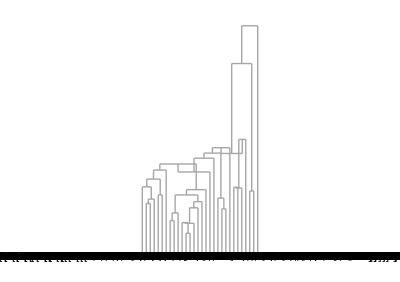

```mathematica
Dendrogram[colors,ClusterDissimilarityFunction->"Centroid"]
```

ClusteringComponents 显示每个元素所在分类的索引

```mathematica
ClusteringComponents[{10,4,5,6,11},2]
```

{1,2,2,2,1}

```mathematica
FindClusters[{10,4,5,6,11},2]
```

{{10,11},{4,5,6}}

Nearest 找出与给定数据最近的元素

```mathematica
Nearest[{1,2,10,12,3,1,13,25},8]
```

{10}

Nearest 找出与给定数据最近的5个元素

```mathematica
Nearest[{1,2,10,12,3,1,13,25},8,5]
```

{10,12,3,13,2}

## 无监督聚类和有监督学习的分类

ClusterClassify 通过聚类自动标记数据并生成 ClassifierFunction

有标记数据

-10 | Class A
-9 | Class A
-8 | Class A
-7 | Class A
5 | Class B
6 | Class B
7 | Class B
8 | Class B

无标记数据进行聚类

{-10,-9,-8,-7}
{5,6,7,8}

从聚类函数中

```mathematica
c=ClusterClassify[{-10,-9,-8,-7,5,6,7,8}]
```

```mathematica
c/@{-10,-9,-8,-7,5,6,7,8}
```

为新数据分类

```mathematica
c[-4]
```

```mathematica
c[10]
```

通过聚类把颜色分为三组，并且使用新生成的分类器预测颜色

{RGBColor[0.42880669394347026, 0.6313263749218327, 0.04017197523732796],RGBColor[0.5322844567602745, 0.20934524063040416, 0.4625304315913801],RGBColor[0.1216024506457376, 0.9259363652997707, 0.7560869383761055],RGBColor[0.5370012775490045, 0.6769216710609116, 0.010526530822881242],RGBColor[0.8614617783949217, 0.7459514645065781, 0.522653181119024],RGBColor[0.4896967720344436, 0.9691422592169678, 0.7118387212463448],RGBColor[0.9081392039259952, 0.13651539486568853, 0.7420036662522862],RGBColor[0.9921331973646756, 0.45862022554859516, 0.5922318171482548],RGBColor[0.04937458577673093, 0.41734508919177715, 0.21098380833470554],RGBColor[0.2062322825901335, 0.25754211034864105, 0.7661189387600418],RGBColor[0.6932470433510147, 0.4401657069396381, 0.978662712158674],RGBColor[0.6448783012102666, 0.5036808006397588, 0.017099857793755113],RGBColor[0.5245801105298751, 0.1788358267934027, 0.30155360286361743],RGBColor[0.8945685988059731, 0.4035929890094343, 0.04704565152941487],RGBColor[0.26211417290451333, 0.6403715671807986, 0.8549799894437393],RGBColor[0.8995137310201922, 0.8106098881046664, 0.7404162493611282],RGBColor[0.24537284677038218, 0.9550392767284799, 0.7449269427153833],RGBColor[0.7253565751873425, 0.6562957841435455, 0.2938937613517303],RGBColor[0.8307635507963509, 0.7730250025889249, 0.10357489678836473],RGBColor[0.7751431736716752, 0.11962603565080987, 0.7604249690550002],RGBColor[0.9760011504311707, 0.42411390523039016, 0.5711718606945924],RGBColor[0.5052094526238524, 0.058709816169977946, 0.9751608167326571],RGBColor[0.0734088422797694, 0.5296238959126476, 0.04428185023975262],RGBColor[0.5326041643350432, 0.6981088213370117, 0.4769251772272436],RGBColor[0.7992215969205407, 0.42737139553088066, 0.6752697021860832],RGBColor[0.7627986832946148, 0.45616796872766496, 0.5821840426452396],RGBColor[0.8258027801385157, 0.35916809045062004, 0.9935613732820141],RGBColor[0.7402777334420556, 0.3558994583717976, 0.897170114623848],RGBColor[0.8575046726708695, 0.5376520318193585, 0.10576367576615575],RGBColor[0.0229704286049639, 0.06727965634325117, 0.8166447182490686]}

```mathematica
c=ClusterClassify[colors,3]
```

更详细的分类器

```mathematica
Information[c]
```

检视颜色的聚类

```mathematica
GroupBy[colors,c]
```

为新颜色进行分类

```mathematica
c[{"White","Purple","Blue","Green","Yellow","Orange","Red"}]
```